```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/Fluorescence"];
Table[A[i]=Cases[Import[#[[i]],"Table"],{_Real,_Real}],{i,1,Length[#]}]&@FileNames["*.TXT"];
```

```mathematica
TableForm[Transpose[{Range[Length[#]],#}]&@FileNames["*.TXT"]]
```

1 | 0_5_2ND.TXT
2 | 0_5EM2ND.TXT
3 | 0_5EMIT'.TXT
4 | 0_5EMIT.TXT
5 | 0_5'.TXT
6 | 0_5.TXT
7 | 10MLACOH.TXT
8 | 20MLACOH.TXT
9 | 5MLACOH.TXT
10 | BACK'.TXT
11 | BACK.TXT
12 | PH_MIN'.TXT
13 | PH_MIN.TXT
14 | STANDARD.TXT
15 | UNKNOWN.TXT

```mathematica
A[14]
```

{}

```mathematica
Fit[{#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"),{1,x},x]
```

14.1588+2734.31 x

```mathematica
Solve[14.158799999999832+2734.3137499999993 x==272.407,x]
```

{{x→0.0944472}}

```mathematica
LinearModelFit[{#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"),{1,x},x]["RSquared"]
```

0.999613

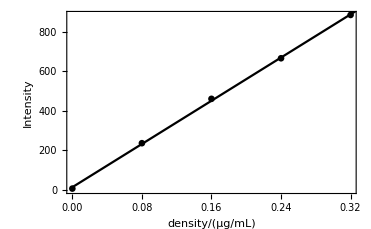

```mathematica
Show[
ListPlot[#,Axes->False,Frame->True,PlotStyle->Black,FrameLabel->{"density/(μg/mL)","Intensity"}],
Plot[14.158799999999832+2734.3137499999993 x,{x,0,1},PlotStyle->Black]
]&@({#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"))
```

```mathematica
Export["Standardcurve.eps",%]
```

Standardcurve.eps

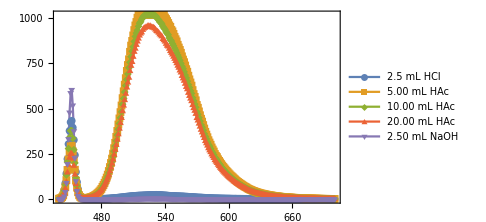

```mathematica
ListLinePlot[{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])},PlotRange->All,PlotMarkers->{Automatic,8},ImageSize->Medium,Frame->True,Axes->False,PlotLegends->{"2.5 mL HCl","5.00 mL HAc","10.00 mL HAc","20.00 mL HAc","2.50 mL NaOH"},ImageSize->Large]
```

```mathematica
Position[#,1]&/@(PeakDetect[#,0,2,200]&/@(#2&@@@Transpose/@{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])}))
```

{{{13}},{{13}},{{12},{83}},{{13},{85},{87}},{{13}}}

```mathematica
functionlist=Interpolation[#][x]&/@{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])};
```

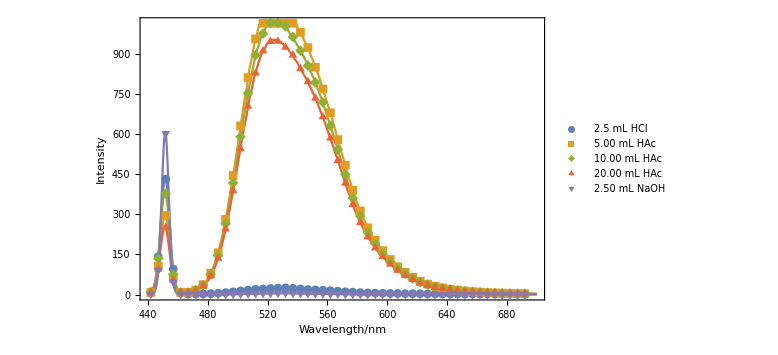

```mathematica
Show[Plot[functionlist,{x,440,700},PlotRange->All,ImageSize->Medium,Frame->True,Axes->False,ImageSize->Large,FrameLabel->{"Wavelength/nm","Intensity"}],ListPlot[Part[#,Table[5i+3,{i,0,50}]]&/@{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])},PlotMarkers->Automatic,PlotLegends->{"2.5 mL HCl","5.00 mL HAc","10.00 mL HAc","20.00 mL HAc","2.50 mL NaOH"},FrameTicks->True],ImageSize->Large]
```

```mathematica
Export["pH.eps",%]
```

pH.eps

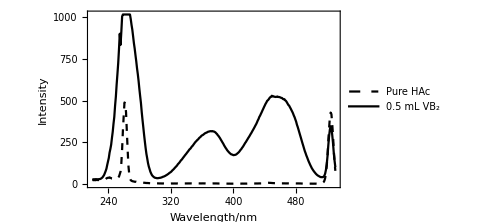

```mathematica
ListLinePlot[{A[11],A[6]},PlotRange->All,ImageSize->Medium,Frame->True,PlotStyle->{{Black,Dashed},{Black}},Axes->False,PlotLegends->{"Pure HAc","0.5 mL VB_2"},FrameLabel->{"Wavelength/nm","Intensity"}]
```

```mathematica
Export["expose.eps",%]
```

expose.eps

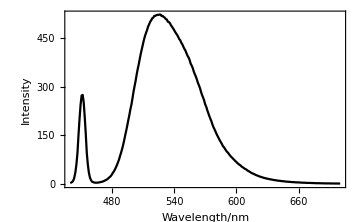

```mathematica
ListLinePlot[A[4],PlotRange->All,ImageSize->Medium,Frame->True,PlotStyle->Black,Axes->False,FrameLabel->{"Wavelength/nm","Intensity"}]
```

```mathematica
Export["emission.eps",%]
```

emission.eps

```mathematica
({#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"))//Transpose//TableForm//TeXForm
```

\begin{array}{ccccc}
 0. & 0.08 & 0.16 & 0.24 & 0.32 \\
 7.154 & 236.915 & 461.473 & 666.732 & 885.971 \\
\end{array}

```mathematica
-Log10/@(ComplexH[{#/60.06,0},{1.8*10^(-5)}]&/@{1/5,10/25,20/25})
```

{3.6271,3.47191,3.31809}

```mathematica
-Log10@ComplexH[{0.6,0},{10000}]
```

0.221875

```mathematica
-Log10@ComplexH[{0,10/40/10},{0}]
```

12.3979

```mathematica
FindFit[Drop[A[4],84],a E^((x-μ)^2/(2 σ^2))(1-E^(k x))+b,{a,σ,μ,k,b},x]
```

Drop::drop: Cannot drop positions 1 through 84 in A[4].

FindFit::fitd: First argument Drop[A[4],84] in FindFit is not a list or a rectangular array.

FindFit[Drop[A[4],84],b+a ⅇ^((x-μ)^2/(2 σ^2)) (1-ⅇ^(k x)),{a,σ,μ,k,b},x]

```mathematica
Drop[A[4],84]
```

{{524.,521.506},{525.,521.359},{526.,522.496},{527.,522.154},{528.,517.867},{529.,518.268},{530.,514.76},{531.,513.079},{532.,508.722},{533.,507.168},{534.,500.293},{535.,499.224},{536.,495.835},{537.,489.656},{538.,484.948},{539.,479.998},{540.,474.977},{541.,469.252},{542.,464.138},{543.,459.471},{544.,453.627},{545.,446.725},{546.,443.147},{547.,435.361},{548.,430.658},{549.,423.093},{550.,416.429},{551.,411.197},{552.,402.821},{553.,395.363},{554.,390.293},{555.,382.309},{556.,371.174},{557.,365.144},{558.,357.615},{559.,347.074},{560.,338.575},{561.,331.374},{562.,322.162},{563.,311.74},{564.,304.197},{565.,295.519},{566.,284.246},{567.,274.28},{568.,266.709},{569.,257.575},{570.,245.764},{571.,238.457},{572.,227.775},{573.,218.688},{574.,209.528},{575.,201.332},{576.,193.621},{577.,183.56},{578.,175.382},{579.,168.841},{580.,161.659},{581.,154.175},{582.,147.856},{583.,141.713},{584.,135.154},{585.,129.838},{586.,124.108},{587.,117.701},{588.,113.928},{589.,109.168},{590.,103.951},{591.,99.762},{592.,96.715},{593.,92.215},{594.,87.976},{595.,84.321},{596.,81.402},{597.,77.9},{598.,74.636},{599.,71.168},{600.,68.56},{601.,65.215},{602.,62.175},{603.,59.926},{604.,57.72},{605.,54.532},{606.,52.338},{607.,50.386},{608.,47.718},{609.,46.331},{610.,44.091},{611.,41.602},{612.,39.882},{613.,37.974},{614.,35.741},{615.,33.68},{616.,32.852},{617.,31.119},{618.,29.594},{619.,27.907},{620.,26.799},{621.,25.519},{622.,24.069},{623.,23.228},{624.,22.033},{625.,21.163},{626.,20.007},{627.,19.107},{628.,18.465},{629.,17.338},{630.,17.06},{631.,16.015},{632.,15.418},{633.,14.942},{634.,14.12},{635.,13.688},{636.,13.028},{637.,12.355},{638.,12.21},{639.,11.354},{640.,11.175},{641.,10.622},{642.,10.34},{643.,9.806},{644.,9.318},{645.,9.138},{646.,8.864},{647.,8.282},{648.,8.055},{649.,7.689},{650.,7.524},{651.,7.28},{652.,7.125},{653.,6.515},{654.,6.476},{655.,6.306},{656.,6.044},{657.,5.769},{658.,5.559},{659.,5.503},{660.,5.517},{661.,5.251},{662.,5.074},{663.,4.642},{664.,4.604},{665.,4.555},{666.,4.413},{667.,4.252},{668.,3.956},{669.,3.955},{670.,3.945},{671.,3.932},{672.,3.69},{673.,3.522},{674.,3.588},{675.,3.321},{676.,3.232},{677.,2.99},{678.,2.977},{679.,3.192},{680.,2.904},{681.,2.891},{682.,2.852},{683.,2.696},{684.,2.625},{685.,2.564},{686.,2.408},{687.,2.478},{688.,2.421},{689.,2.508},{690.,2.329},{691.,2.276},{692.,2.192},{693.,2.273},{694.,2.211},{695.,2.073},{696.,2.133},{697.,2.128},{698.,2.025},{699.,2.018},{700.,2.023}}

```mathematica
-Log10/@(ComplexH[{#/60.06,0},{1.8*10^(-5)}]&/@{1/5,10/25,20/25})

-Log10@ComplexH[{0.6,0},{10000}]

-Log10@ComplexH[{0,10/40/10},{0}]
```

{3.6271,3.47191,3.31809}

0.221875

12.3979

```mathematica
25/0.4*0.0944
```

5.9

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/Chromatography"];
```

```mathematica
FileNames[]
```

{std-01.txt,std-02.txt,std-03.txt,std-04.txt,std-05.txt,std-06.txt,std-07.txt,std-08.txt,std-09.txt,std-10.txt,std-11.txt,std-12.txt}

```mathematica
Table[A[i]=Cases[Import[#[[i]],"Table"],{_Real,_Integer}],{i,1,Length[#]}]&@FileNames["*.TXT"];
```

```mathematica
"Standardextension.eps"~Export~ListLinePlot[Select[#,#[[1]]>1&]&/@A/@Range[6],PlotRange->All,PlotStyle->Thickness[0.002],Frame->True,Axes->False,ImageSize->Medium,PlotLegends->{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000]
```

Standardextension.eps

```mathematica
"Standardextensionsolvent.eps"~Export~ListLinePlot[Select[#,0<#[[1]]<1.16&]&/@A/@Range[6],PlotRange->All,PlotStyle->Thickness[0.002],Frame->True,Axes->False,PlotLegends->{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000]
```

Standardextensionsolvent.eps

```mathematica
"ratio.eps"~Export~ListLinePlot[Select[#,#[[1]]>1&]&/@A/@{7,11,12},PlotRange->All,PlotStyle->Thickness[0.002],Frame->True,Axes->False,ImageSize->Medium,PlotLegends->ToString/@{"80:20","70:30","65:35"}]
```

ratio.eps

```mathematica
#2&@@@Select[#,1.4<#[[1]]<1.5&]&/@A/@Range[6]
```

{{3773,2162,1439,1155,1108,1213,1698,4164,14588},{13877,7410,4431,3128,2628,2531,2729,3814,9535},{15634,8374,5044,3592,3040,2928,3124,4151,9576},{17134,9364,5824,4309,3757,3681,4043,5924,15801},{19536,10956,7108,5497,4944,4932,5519,8511,24059},{37049,19543,11491,7937,6504,6080,6225,7296,12875}}

```mathematica
"Standardextensionmedium.eps"~Export~ListLinePlot[Select[#,1.4<#[[1]]<1.5&]&/@A/@Range[6],PlotStyle->Thickness[0.001],ImageSize->Large,Frame->True,Axes->False]
```

Standardextensionmedium.eps

```mathematica
standard={{{1.312,1257344,344731},{1.548,1097148,273118},{1.777,1015037,232326}},
{{1.321,2767414,756678},{1.558,2409631,602078},{1.789,2231886,513746}},
{{1.320,3228160,886589},{1.559,2809237,706920},{1.792,2607079,607608}},
{{1.317,4069330,1084438},{1.557,3541307,881417},{1.790,3287100,756536}},
{{1.315,5356016,1460194},{1.555,4683383,1168334},{1.790,4354363,10006866}},
{{1.323,6550644,1798912},{1.563,5763248,1416618},{1.798,5363409,1232525}}};
unknown={{{1.324,3319980,973649},{1.566,2887152,765530},{1.802,2676464,659082}},{{1.317,3602989,1028006},{1.559,3134953,832917},{1.796,2908242,707690}},
{{1.326,3778152,1093799},{1.569,3286537,874645},{1.806,3049488,743346}}};
fluid={{{1.324,3319980,973649},{1.566,2887152,765530},{1.802,2676464,659082}},
{{1.472,8408764,2074508},{2.076,7465018,1518307},{2.764,6997466,1190681}},
{{1.470,7600126,1888329},{2.079,6739076,1384434},{2.793,6316958,962652}}};
```

```mathematica
Plot[Normal/@(LinearModelFit[#,{1,x},x]&/@(Transpose[#][[2]]&/@standard//Transpose)),{x,0,
```

{364137.+1.0021×10^6 x,295610.+882395. x,264214.+822552. x}

```mathematica
Normal/@(LinearModelFit[#,{1,x},x]&/@Transpose[{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000,#}]&/@(Transpose[#][[2]]&/@standard//Transpose))
```

{{-1.25726×10^6+1.2573×10^6 x,-2.76725×10^6+2.76733×10^6 x,-3.22796×10^6+3.22806×10^6 x,-4.06909×10^6+4.06921×10^6 x,-5.3557×10^6+5.35586×10^6 x,-6.55024×10^6+6.55044×10^6 x},{-1.09707×10^6+1.09711×10^6 x,-2.40947×10^6+2.40955×10^6 x,-2.80904×10^6+2.80914×10^6 x,-3.54107×10^6+3.54119×10^6 x,-4.68306×10^6+4.68322×10^6 x,-5.76285×10^6+5.76305×10^6 x},{-1.01496×10^6+1.015×10^6 x,-2.23173×10^6+2.23181×10^6 x,-2.60688×10^6+2.60698×10^6 x,-3.28686×10^6+3.28698×10^6 x,-4.35404×10^6+4.3542×10^6 x,-5.36301×10^6+5.36321×10^6 x}}

```mathematica
data=LinearModelFit[#,{1,x},x]&/@(Transpose[{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000,#}]&/@(Transpose[#][[2]]&/@standard//Transpose));
lines=LinearModelFit[#,{1,x},x]&/@(Transpose[{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000,#}]&/@(Transpose[#][[2]]&/@standard//Transpose))//Normal;
dots=Transpose[{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000,#}]&/@(Transpose[#][[2]]&/@standard//Transpose);
```

```mathematica
#["RSquared"]&/@data
```

{0.997614,0.998059,0.998168}

```mathematica
"standardcurve.eps"~Export~Show[ListPlot[dots,PlotMarkers->Automatic,PlotLegends->{"甲酯","丙酯","丁酯"},Frame->True,Axes->False,FrameLabel->{"density/(μg/mL)","Area"},ImageSize->Large],Plot[lines,{x,0,200}]]
```

standardcurve.eps

```mathematica
Transpose[{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000}]
```

{{40.},{80.},{100.},{120.},{160.},{200.}}

```mathematica
Transpose[Transpose[#][[2]]&/@unknown]//TableForm//TeXForm
```

\begin{array}{ccc}
 3319980 & 3602989 & 3778152 \\
 2887152 & 3134953 & 3286537 \\
 2676464 & 2908242 & 3049488 \\
\end{array}

```mathematica
Transpose[x/.Partition[Flatten@Solve[lines[[#1]]==Transpose[Transpose[#][[2]]&/@unknown][[#1]][[#2]],x]&@@@Tuples[{1,2,3},2],3]]
```

{{99.9815,99.6087,99.4792},{108.544,108.116,108.015},{113.843,113.321,113.217}}

```mathematica
Mean/@Transpose[x/.Partition[Flatten@Solve[lines[[#1]]==Transpose[Transpose[#][[2]]&/@unknown][[#1]][[#2]],x]&@@@Tuples[{1,2,3},2],3]]
```

{99.6898,108.225,113.46}

```mathematica
Transpose[x/.Partition[Flatten@Solve[lines[[#1]]==Transpose[Transpose[#][[2]]&/@unknown][[#1]][[#2]],x]&@@@Tuples[{1,2,3},2],3]]//TableForm//TeXForm
```

\begin{array}{ccc}
 99.9815 & 99.6087 & 99.4792 \\
 108.544 & 108.116 & 108.015 \\
 113.843 & 113.321 & 113.217 \\
\end{array}

```mathematica
Transpose[Transpose[#][[2]]&/@standard]//TableForm//TeXForm
```

\begin{array}{cccccc}
 1257344 & 2767414 & 3228160 & 4069330 & 5356016 & 6550644 \\
 1097148 & 2409631 & 2809237 & 3541307 & 4683383 & 5763248 \\
 1015037 & 2231886 & 2607079 & 3287100 & 4354363 & 5363409 \\
\end{array}

```mathematica
{{0.2,0.4,0.5,0.6,0.8,1.0}/5*1000}//TableForm//TeXForm
```

\begin{array}{cccccc}
 40. & 80. & 100. & 120. & 160. & 200. \\
\end{array}

```mathematica
#[[1]]/#&/@(Transpose[#][[2]]&/@standard)//N//Transpose//TableForm//TeXForm
```

\begin{array}{cccccc}
 1. & 1. & 1. & 1. & 1. & 1. \\
 1.14601 & 1.14848 & 1.14912 & 1.1491 & 1.14362 & 1.13662 \\
 1.23872 & 1.23994 & 1.23823 & 1.23797 & 1.23003 & 1.22136 \\
\end{array}

```mathematica
#[[1]]/#&/@(Transpose[#][[2]]&/@standard)//N//Mean
```

{1.,1.14549,1.23438}

```mathematica
lines
```

{15237.7+33053.5 x,-14101.9+29126.5 x,-24641.3+27152.5 x}

```mathematica
correction=#[[1]]/#&/@(Transpose[#][[2]]&/@standard)//N//Mean;
```

```mathematica
(Mean[Transpose[#][[2]]&/@unknown]*correction)/(Mean[Transpose[#][[2]]&/@unknown].correction)
```

{0.334181,0.33299,0.332829}

```mathematica
Transpose[#][[2]]&/@unknown.correction
```

{8.0088×10^6,8.69591×10^6,9.11784×10^6}

```mathematica
Transpose[#][[2]]&/@unknown
```

{{3319980,2887152,2676464},{3602989,3134953,2908242},{3778152,3286537,3049488}}

```mathematica
#/Total[#]&[Mean/@Transpose[x/.Partition[Flatten@Solve[lines[[#1]]==Transpose[Transpose[#][[2]]&/@unknown][[#1]][[#2]],x]&@@@Tuples[{1,2,3},2],3]]]
```

{0.310197,0.336756,0.353046}

```mathematica
SetDirectory["F:\\GitHub\\Elucate\\中级化学实验报告\\data\\Gas Chromatography"];
```

```mathematica
Table[A[i]=Cases[Import[#[[i]],"Table"],{_Real,_Integer}],{i,1,Length[#]}]&@FileNames["*.TXT"];
```

```mathematica
TableForm[Transpose[{Range[Length[#]],#}]&@FileNames["*.TXT"]]
```

1 | MixStandardSolution-2.TXT
2 | MixStandardSolution-3.TXT
3 | MixStandardSolution-4.TXT
4 | qualitative-1.TXT
5 | qualitative-2.TXT
6 | qualitative-3.TXT
7 | qualitative-4.TXT
8 | Temperature-1.TXT
9 | Temperature-2.TXT
10 | Temperature-3.TXT
11 | Temperature-4.TXT
12 | Unknown-1.TXT
13 | Unknown-2.TXT
14 | Unknown-3.TXT
15 | Unknown-4.TXT

```mathematica
"Temperature.eps"~Export~ListLinePlot[(Select[#,1.8<#[[1]]<2.7&]&/@A/@Table[i,{i,8,10}]),PlotRange->All,Frame->True,Axes->False,ImageSize->Medium,PlotStyle->{{DotDashed,Black,Thickness[0.0025]},{Dashed,Black,Thickness[0.003]},{Black,Thickness[0.0025]},{Dotted,Black,Thickness[0.005]}},PlotLegends->{"90^oC","80^oC","70^oC"},FrameLabel->{"time/min","Intensity"}]
```

Temperature.eps

```mathematica
"Unknown.eps"~Export~ListLinePlot[(Select[#,1.9<#[[1]]<2.7&]&/@A/@Table[i,{i,12,15}]),PlotRange->All,Frame->True,Axes->False,ImageSize->Medium,PlotStyle->{{DotDashed,Black,Thickness[0.0025]},{Dashed,Black,Thickness[0.003]},{Black,Thickness[0.0025]},{Dotted,Black,Thickness[0.005]}},PlotLegends->{"第一次","第二次","第三次","第四次"},FrameLabel->{"time/min","Intensity"}]
```

Unknown.eps

```mathematica
"qualitative.eps"~Export~ListLinePlot[(Select[#,1.9<#[[1]]<2.7&]&/@A/@Table[i,{i,4,7}]),PlotRange->All,Frame->True,Axes->False,ImageSize->Medium,PlotStyle->{{DotDashed,Black,Thickness[0.0025]},{Dashed,Black,Thickness[0.003]},{Black,Thickness[0.0025]},{Dotted,Black,Thickness[0.005]}},PlotLegends->{"正丁醇","异丁醇","仲丁醇","叔丁醇"},FrameLabel->{"time/min","Intensity"}]
```

qualitative.eps

```mathematica
"MixStandard.eps"~Export~ListLinePlot[(Select[#,1.9<#[[1]]<2.7&]&/@A/@Table[i,{i,1,3}]),PlotRange->All,Frame->True,Axes->False,ImageSize->Medium,PlotStyle->{{DotDashed,Black,Thickness[0.0025]},{Dashed,Black,Thickness[0.003]},{Black,Thickness[0.0025]},{Dotted,Black,Thickness[0.005]}},PlotLegends->{"正丁醇","异丁醇","仲丁醇","叔丁醇"},FrameLabel->{"time/min","Intensity"}]
```

MixStandard.eps

```mathematica
program[data_]:=Module[{PeakList,result={},operation},
operation[list_,peakinfo_]:=Module[{point,i=peakinfo[[1]],k=peakinfo[[1]]},
point=list[[peakinfo[[1]]]];
While[point[[2]]>peakinfo[[2]]/2,point=list[[++i]]];
point=list[[peakinfo[[1]]]];
While[point[[2]]>peakinfo[[2]]/2,point=list[[--k]]];
AppendTo[result,{list[[k]],list[[peakinfo[[1]]]],list[[i]]}]
];
PeakList=FindPeaks[Last/@data,0,0,100000];
operation[data,#]&/@PeakList;
result
]
(*该program为寻找气相色谱中大于100000的峰的峰位及半峰点的信息*)
```

```mathematica
(#[[3,1]]-#[[1,1]]&/@program[A[#]][[{3,4}]])&/@{8,9,10,11}
```

{{0.02667,0.02666},{0.026,0.02533},{0.026,0.02466},{0.02667,0.02733}}

```mathematica
FindPeaks[Last/@A[8],0,0,100000]
```

{{2802,15359367},{2897,1988969},{3036,1655778},{3101,2013407},{3213,1948913}}

```mathematica
program[A[8]][[{3,4}]]
```

{{{2.0145,794077},{2.02383,1655778},{2.04117,796354}},{{2.05717,977274},{2.06717,2013407},{2.08383,960182}}}

```mathematica
table1={{{2.083,2588767},{2.086,2503002},{2.086,2798238}},{{2.248,2228601},{2.251,2145371},{2.252,2457889}},{{2.334,2628089},{2.337,2524540},{2.338,2940840}},{{2.481,2510860},{2.484,2413107},{2.486,2852094}}};
table2={{{2.113,4383773},{2.119,2623718},{2.103,3693649},{2.112,2170869}},{{2.277,1306267},{2.283,740094},{2.267,767346},{2.276,591332}},{{2.372,6184906},{2.371,3457951},{2.355,3543378},{2.362,2661866}},{{2.518,3815628},{2.515,2086877},{2.5,2116732},{2.505,1527732}}};
```

```mathematica
Flatten/@table2//TableForm//TeXForm
```

\begin{array}{cccccccc}
 2.113 & 4383773 & 2.119 & 2623718 & 2.103 & 3693649 & 2.112 & 2170869 \\
 2.277 & 1306267 & 2.283 & 740094 & 2.267 & 767346 & 2.276 & 591332 \\
 2.372 & 6184906 & 2.371 & 3457951 & 2.355 & 3543378 & 2.362 & 2661866 \\
 2.518 & 3815628 & 2.515 & 2086877 & 2.5 & 2116732 & 2.505 & 1527732 \\
\end{array}

```mathematica
#[[2]]/@table1//TableForm
```

Part::partw: Part 2 of #1 does not exist.

#1⟦2⟧[{{2.083,2588767},{2.086,2503002},{2.086,2798238}}]
#1⟦2⟧[{{2.248,2228601},{2.251,2145371},{2.252,2457889}}]
#1⟦2⟧[{{2.334,2628089},{2.337,2524540},{2.338,2940840}}]
#1⟦2⟧[{{2.481,2510860},{2.484,2413107},{2.486,2852094}}]

```mathematica
#/Last[#]&[Last/@Total/@table1/3]//N
```

{1.01465,0.878576,1.04082,1.}

```mathematica
"MixStandardFront.eps"~Export~ListLinePlot[(Select[#,#[[1]]<2.1&]&/@A/@Table[i,{i,1,3}]),PlotRange->{Automatic,{0,100000}},Frame->True,Axes->False,ImageSize->Medium,PlotStyle->{{DotDashed,Black,Thickness[0.0025]},{Dashed,Black,Thickness[0.003]},{Black,Thickness[0.0025]},{Dotted,Black,Thickness[0.005]}},PlotLegends->{"第一次","第二次","第三次","第四次"},FrameLabel->{"time/min","Intensity"}]
```

MixStandardFront.eps

```mathematica
Solve[Log[#2*1000/10^5]==x/8.314(1/298.15-1/(#1+273.15)),x]&@@@{{117.6,0.86},{99.4,2.32},{107.84,1.39},{82.3,5.52}}
```

{{{x→-49747.8}},{{x→-46715.4}},{{x→-48746.4}},{{x→-44543.7}}}

```mathematica
{1.0146534344316487,0.8785760554090304,1.0408186098334362,1.}
```

{{0.0005,-512},{0.00117,-512},{0.00183,-513},{0.0025,-513},{0.00317,-513},{0.00383,-513},{0.0045,-513},{0.00517,-512},{0.00583,-511},4355,{2.90983,-64},{2.9105,-66},{2.91117,-67},{2.91183,-69},{2.9125,-71},{2.91317,-73},{2.91383,-74},{2.9145,-76},{2.91517,-77}}
 |  |  |  |

```mathematica
Divide@@@Transpose[{Last/@Total/@Transpose[Drop[table2//Transpose,1]]/3,{1.0146534344316487,0.8785760554090304,1.0408186098334362,1.}}]
```

{2.78855×10^6,796278.,3.09474×10^6,1.91045×10^6}

```mathematica
#/Last[#]&[Times@@@Transpose[{Last/@Total/@Transpose[Drop[table2//Transpose,1]]/3,{0.9855581877177041,1.1382053879609084,0.9607822059984414,1.}}]]//N
```

{1.45963,0.416802,1.6199,1.}

```mathematica
1/{1.0146534344316487,0.8785760554090304,1.0408186098334362,1.}
```

{0.985558,1.13821,0.960782,1.}

```mathematica
Last/@Total/@Transpose[Drop[table2//Transpose,1]]/3
```

{2829412,2098772/3,3221065,1910447}

```mathematica
{1.4596323075315485,0.4168018616413665,1.6199046277464748,0.9999999999999999}*0.4050
```

```mathematica
{0.5911510845502772*1.3878/0.8148,0.16880475396475345*1.3955/0.8148,0.6560613742373224*0.8063/0.8148,0.40499999999999997}
```

{1.00687,0.28911,0.649217,0.405}

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/AtomicSpectrophy"];
```

```mathematica
StC={{0.00,0.000},{0.20,0.115},{0.40,0.211},{0.60,0.314},{0.80,0.413},{1.00,0.461}};
```

```mathematica
StA={Table[i,{i,0,2,0.5}],{0.097,0.198,0.290,0.372,0.449}}//Transpose;
```

```mathematica
Sr={{0.00,0.50,2.00,3.00,4.00},{0.149,0.153,0.148,0.145,0.142}}//Transpose;
```

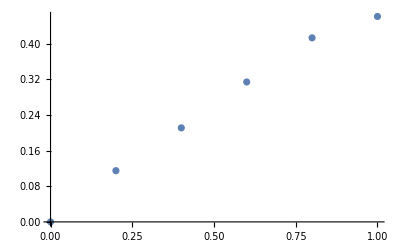

```mathematica
ListPlot[StC]
```

```mathematica
StC1={{0.00,0.000},{0.20,0.103},{0.40,0.211},{0.60,0.314},{0.80,0.396},{1.00,0.461}};
```

```mathematica
Export["StandardCurve.eps",Show[ListPlot[{StC1,StC},PlotRange->All,ImageSize->Medium,Frame->True,PlotMarkers->Automatic,Axes->False,PlotLegends->{"第一次数据","引入第二次数据"},FrameLabel->{"镁标准浓度/(μg/mL)","吸光度"}],Plot[Evaluate[{LinearModelFit[StC1,{1,x},x]//Normal,LinearModelFit[StC,{1,x},x]//Normal}],{x,0,1.0},PlotStyle->{{Thickness[0.003]},{Thickness[0.003],Dashed}}]]]
```

StandardCurve.eps

```mathematica
,
```

```mathematica
LinearModelFit[StC1,{1,x},x]["RSquared"]
```

0.99243

```mathematica
LinearModelFit[StC,{1,x},x]["RSquared"]
```

0.989585

```mathematica
Export["StandardAddition.eps",Show[ListPlot[StA,PlotRange->All,ImageSize->Medium,Frame->True,PlotMarkers->"×",Axes->False,FrameLabel->{"镁标准溶液加入量/mL","吸光度"},PlotStyle->{Black,PointSize[0.1]}],Plot[Evaluate[LinearModelFit[StA,{1,x},x]//Normal],{x,0,2.0}],PlotStyle->Black]]
```

StandardAddition.eps

```mathematica
LinearModelFit[StA,{1,x},x]["RSquared"]
```

0.996865

```mathematica
Export["Sr.eps",Show[ListPlot[Sr,PlotRange->All,ImageSize->Medium,Frame->True,PlotMarkers->"×",Axes->False,FrameLabel->{"Sr溶液加入量/mL","吸光度"},PlotStyle->{Black,PointSize[0.1]}],Plot[Evaluate[Interpolation[Sr,Method->"Spline"][x]],{x,0,4.0},PlotStyle->{Black,Thickness[0.003]}]]]
```

Sr.eps

```mathematica
Manipulate[Sr]
```

```mathematica
LinearModelFit[StC1,{1,x},x]//Normal
```

0.0127143+0.469571 x

```mathematica
LinearModelFit[StC1,{1,x},x]["ParameterConfidenceIntervals"]
```

{{-0.0217606,0.0471891},{0.412638,0.526505}}

```mathematica
LinearModelFit[StC,{1,x},x]["ParameterConfidenceIntervals"]
```

{{-0.024203,0.0571553},{0.404535,0.538894}}

```mathematica
x/.Solve[Evaluate[LinearModelFit[StC,{1,x},x]//Normal]==#,x]&[Mean[{0.144,0.139}]]*5
```

{1.32521}

```mathematica
x/.Solve[Evaluate[LinearModelFit[StC1,{1,x},x]//Normal]==#,x]&[Mean[{0.144,0.139}]]
```

{0.274262}

```mathematica
x/.Solve[Evaluate[LinearModelFit[StC1,{1,x},x]//Normal]==#,x]&[Mean[{0.144,0.139}]]
```

```mathematica
LinearModelFit[StA,{1,x},x]//Normal
```

0.1056+0.1756 x

```mathematica
x/.Solve[Evaluate[LinearModelFit[StA,{1,x},x]//Normal]==0,x]
```

{-0.601367}

```mathematica
%*5
```

{-0.135382}

```mathematica
0.6013667425968098*10/50
```

0.120273

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/IR"];
```

```mathematica
FileNames[]
```

{WalterFengBenzoicAcid.CSV,WalterFengEthylAcetate.CSV,._WalterFengPlasticBag.CSV,WalterFengPlasticBag.CSV,WalterFengPlasticBag.SPA,WalterFengUnknon.CSV}

```mathematica
Table[A[i]=Cases[Import[#[[i]],"Data"],{_Real,_Real}],{i,1,Length[#]}]&@FileNames["*.csv"]
```

{{{399.692,0.},{400.174,30.5195},{400.656,30.8578},{401.138,31.2055},{401.62,31.5144},{402.102,31.7501},{402.584,31.9081},{403.067,32.0153},{403.549,32.1142},{404.031,32.239},{404.513,32.3985},{404.995,32.5702},7445,{3994.99,19.1075},{3995.47,19.1024},{3995.95,19.0992},{3996.43,19.0979},{3996.92,19.0981},{3997.4,19.0991},{3997.88,19.1},{3998.36,19.1002},{3998.84,19.0993},{3999.33,19.0971},{3999.81,19.0936},{4000.29,0.}},3,{1}}
 |  |  |  |

```mathematica
"BenzoicAcid.eps"~Export~ListLinePlot[A[1],PlotRange->{{450,4000},{5,30}},ImageSize->Large,Frame->True,PlotStyle->{Black,Thickness[0.001]},Axes->False,FrameLabel->{"Wavenumber/cm^-1","Transmittance/%"},ScalingFunctions->{"Reverse",Identity}]
```

BenzoicAcid.eps

```mathematica
"EthylAcetate.eps"~Export~ListLinePlot[A[2],PlotRange->{{400,4000},Automatic},ImageSize->Large,Frame->True,PlotStyle->{Black,Thickness[0.001]},Axes->False,FrameLabel->{"Wavenumber/cm^-1","Transmittance/%"},ScalingFunctions->{"Reverse",Identity}]
```

EthylAcetate.eps

```mathematica
"plasticbag.eps"~Export~ListLinePlot[A[4],PlotRange->{{400,4000},{75,105}},ImageSize->Large,Frame->True,PlotStyle->{Black,Thickness[0.001]},Axes->False,FrameLabel->{"Wavenumber/cm^-1","Transmittance/%"},ScalingFunctions->{"Reverse",Identity}]
```

plasticbag.eps

```mathematica
A[4]
```

{{399.681,0.},{400.164,103.394},{400.646,107.875},{401.128,111.486},{401.61,113.488},7459,{3998.26,103.906},{3998.74,103.91},{3999.22,103.912},{3999.71,103.913},{4000.19,103.912}}
 |  |  |  |

```mathematica
FileNames["*.csv"]
```

{WalterFengBenzoicAcid.CSV,WalterFengEthylAcetate.CSV,._WalterFengPlasticBag.CSV,WalterFengPlasticBag.CSV,WalterFengUnknon.CSV}

```mathematica
"unknown.eps"~Export~ListLinePlot[A[5],PlotRange->{{400,4000},Automatic},ImageSize->Large,Frame->True,PlotStyle->{Black,Thickness[0.001]},Axes->False,FrameLabel->{"Wavenumber/cm^-1","Transmittance/%"},ScalingFunctions->{"Reverse",Identity}]
```

unknown.eps

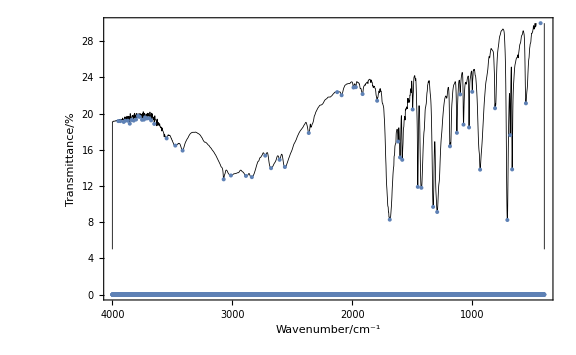

```mathematica
Show[ListLinePlot[A[1],PlotRange->{{450,4000},{5,30}},ImageSize->Large,Frame->True,PlotStyle->{Black,Thickness[0.001]},Axes->False,FrameLabel->{"Wavenumber/cm^-1","Transmittance/%"},ScalingFunctions->{"Reverse",Identity}],ListPlot[Transpose[{First/@A[1],PeakDetect[-Last/@A[1],10,0，10]*Last/@A[1]}],ScalingFunctions->{"Reverse",Identity},PlotStyle->PointSize[0.005]],ImageSize->Large]
```

```mathematica
A[1]
```

{{399.692,0.},{400.174,30.5195},{400.656,30.8578},{401.138,31.2055},{401.62,31.5144},{402.102,31.7501},{402.584,31.9081},{403.067,32.0153},{403.549,32.1142},{404.031,32.239},{404.513,32.3985},{404.995,32.5702},{405.477,32.7103},7444,{3994.99,19.1075},{3995.47,19.1024},{3995.95,19.0992},{3996.43,19.0979},{3996.92,19.0981},{3997.4,19.0991},{3997.88,19.1},{3998.36,19.1002},{3998.84,19.0993},{3999.33,19.0971},{3999.81,19.0936},{4000.29,0.}}
 |  |  |  |

```mathematica
Manipulate[Show[ListLinePlot[A[1],PlotRange->{{450,4000},{5,30}},ImageSize->Large,Frame->True,PlotStyle->{Black,Thickness[0.001]},Axes->False,FrameLabel->{"Wavenumber/cm^-1","Transmittance/%"},ScalingFunctions->{"Reverse",Identity}],ListPlot[Transpose[{First/@A[1],PeakDetect[-Last/@A[1],x,0，10]*Last/@A[1]}],ScalingFunctions->{"Reverse",Identity},PlotStyle->PointSize[0.005]],ImageSize->Large],{x,1,20}]
```

ListLinePlot::lpn: «56417» is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

PeakDetect::arg: The argument -«56417» at position 1 is not a consistent list of real values.

Transpose::nmtx: The first two levels of {«56417»,«56417» PeakDetect[-«56417»,12.98,0]} cannot be transposed.

PeakDetect::arg: The argument -1. «56417» at position 1 is not a consistent list of real values.

Transpose::nmtx: The first two levels of {«56417»,«56417» PeakDetect[-1. «56417»,12.98,0]} cannot be transposed.

PeakDetect::arg: The argument -1. «56417» at position 1 is not a consistent list of real values.

General::stop: Further output of PeakDetect::arg will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {«56417»,«56417» PeakDetect[-1. «56417»,12.98,0.]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{«56417»,«56417» PeakDetect[-1. «56417»,12.98,0.]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[«56417»,PlotRange→{{450,4000},{5,30}},ImageSize→Large,Frame→True,PlotStyle→{GrayLevel[0],Thickness[0.001]},Axes→False,FrameLabel→{Wavenumber/cm^-1,Transmittance/%},ScalingFunctions→{Reverse,Identity}],ListPlot[Transpose[{«56417»,«56417» PeakDetect[-«56417»,12.98,0]}],ScalingFunctions→{Reverse,Identity},PlotStyle→PointSize[0.005]],ImageSize→Large].

```mathematica
Reverse[Select[PeakDetect[-Last/@A[1],13,0，10]*(First/@A[1]),0<#<3800&]]
```

{3780.44,3752.47,3736.56,3676.78,3650.74,3547.56,3475.24,3414.49,3072.18,3011.91,2886.55,2837.38,2725.52,2677.31,2605.95,2562.08,2362.95,2125.74,2089.1,1989.78,1970.98,1914.57,1793.07,1687.96,1602.14,1583.82,1497.04,1454.13,1424.23,1326.36,1292.61,1186.06,1128.2,1100.72,1073.24,1026.95,1000.43,934.864,810.472,707.777,667.76,553.011,430.548,399.692}

```mathematica
"BenzoicAcidAnalysis.eps"~Export~Show[ListLinePlot[A[1],PlotRange->{{450,4000},{5,30}},ImageSize->Large,Frame->True,PlotStyle->{Black,Thickness[0.001]},Axes->False,FrameLabel->{"Wavenumber/cm^-1","Transmittance/%"},ScalingFunctions->{"Reverse",Identity}],ListPlot[Callout[#,#[[1]],Automatic]&/@Select[Transpose[{First/@A[1],PeakDetect[-Last/@A[1],13,0，10]*Last/@A[1]}],#[[1]]<3800&&#[[2]]>0&],ScalingFunctions->{"Reverse",Identity},PlotStyle->PointSize[0.007],ImageSize->Large]]
```

BenzoicAcidAnalysis.eps

```mathematica
"EthylAcetateAnalysis.eps"~Export~Show[ListLinePlot[A[2],PlotRange->{{400,4000},Automatic},ImageSize->Large,Frame->True,PlotStyle->{Black,Thickness[0.001]},Axes->False,FrameLabel->{"Wavenumber/cm^-1","Transmittance/%"},ScalingFunctions->{"Reverse",Identity}],ListPlot[Callout[#,#[[1]],Automatic]&/@Select[Transpose[{First/@A[2],PeakDetect[-Last/@A[2],16,0，100]*Last/@A[2]}],#[[1]]<3800&&#[[2]]>0&],ScalingFunctions->{"Reverse",Identity},PlotStyle->PointSize[0.007],ImageSize->Large]]
```

EthylAcetateAnalysis.eps

```mathematica
"plasticbagAnalysis.eps"~Export~Show[ListLinePlot[A[4],PlotRange->{{400,4000},{75,105}},ImageSize->Large,Frame->True,PlotStyle->{Black,Thickness[0.001]},Axes->False,FrameLabel->{"Wavenumber/cm^-1","Transmittance/%"},ScalingFunctions->{"Reverse",Identity}],ListPlot[Callout[#,#[[1]],Automatic]&/@Select[Transpose[{First/@A[4],PeakDetect[-Last/@A[4],21,0]*Last/@A[4]}],#[[1]]<3800&&#[[2]]>0&],ScalingFunctions->{"Reverse",Identity},PlotStyle->PointSize[0.007],ImageSize->Large,PlotRange->All]]
```

plasticbagAnalysis.eps

```mathematica
"unknownAnalysis.eps"~Export~Show[ListLinePlot[A[5],PlotRange->{{400,4000},Automatic},ImageSize->Large,Frame->True,PlotStyle->{Black,Thickness[0.001]},Axes->False,FrameLabel->{"Wavenumber/cm^-1","Transmittance/%"},ScalingFunctions->{"Reverse",Identity}],ListPlot[Callout[#,#[[1]],Automatic]&/@Select[Transpose[{First/@A[5],PeakDetect[-Last/@A[5],17,0]*Last/@A[5]}],#[[1]]<3800&&#[[2]]>0&],ScalingFunctions->{"Reverse",Identity},PlotStyle->PointSize[0.007],ImageSize->Large,PlotRange->All]]
```

unknownAnalysis.eps

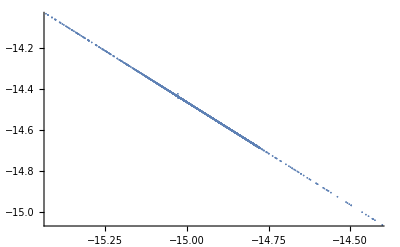

```mathematica
ListPlot[Re[InverseFourier[A[1]]],PlotRange->Automatic]
```

```mathematica
Plot[InverseFourierTransform[Interpolation[A[1],Method->"Hermite"][x],x,t],{t,0,1000}]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in x in the region {{-∞,∞}}. NIntegrate obtained 1.00884×10^62+7.43394×10^61 ⅈ and 1.01651×10^63 for the integral and error estimates.

$Aborted

```mathematica
MapThread[Export,{{"BenzoicAcidFourier.eps","EthylAcetateFourier.eps","plasticbagFourier.eps","unknownFourier.eps"},ListPlot[Re[InverseFourier[Last/@A[#]]]]&/@{1,2,4,5}}]
```

{BenzoicAcidFourier.eps,EthylAcetateFourier.eps,plasticbagFourier.eps,unknownFourier.eps}

```mathematica
Append[Range[25],28]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,28}

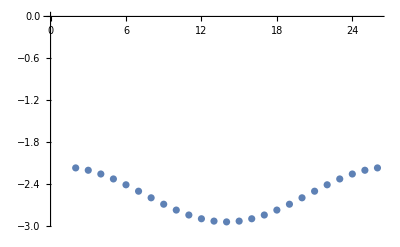

```mathematica
ListPlot[Re/@Fourier[Append[Range[25],28]]]
```

```mathematica
Plot[Interpolation[A[1],Method->"Hermite"][x],{x,400,4000}]



Fourier[AppendTo[Range[25],28]]
```

$Aborted

Set::write: Tag Range in Range[25] is Protected.

{69.229+0. ⅈ,-2.16868-21.091 ⅈ,-2.20221-10.526 ⅈ,-2.25592-6.9826 ⅈ,-2.3267-5.18049 ⅈ,-2.41042-4.06035 ⅈ,-2.50223-3.26717 ⅈ,-2.59679-2.64804 ⅈ,-2.6886-2.12654 ⅈ,-2.77232-1.66089 ⅈ,-2.8431-1.227 ⅈ,-2.89681-0.810677 ⅈ,-2.93034-0.403434 ⅈ,-2.94174-1.65477×10^-15 ⅈ,-2.93034+0.403434 ⅈ,-2.89681+0.810677 ⅈ,-2.8431+1.227 ⅈ,-2.77232+1.66089 ⅈ,-2.6886+2.12654 ⅈ,-2.59679+2.64804 ⅈ,-2.50223+3.26717 ⅈ,-2.41042+4.06035 ⅈ,-2.3267+5.18049 ⅈ,-2.25592+6.9826 ⅈ,-2.20221+10.526 ⅈ,-2.16868+21.091 ⅈ}

```mathematica
Graphics3D[Point[#]&/@Drop[#,1]&/@Cases[ImportString["%nprocshared=1\n%mem=1GB\n%chk=DFT-6-31gd-cyclohexanene-opt.chk\n# opt freq b3lyp/6-31g(d') geom=connectivity\n\nDFT-6-31gd-cyclohexanene-opt.com\n\n0 1\n C                 -4.02419411   -1.35882655    0.26938459\n C                 -2.50171610   -1.26810686    0.03922188\n C                 -2.03962244    0.19745501   -0.04711753\n C                 -2.53480556    0.92237803    1.20783202\n C                 -4.06792071    1.02641214    1.12070301\n C                 -4.70731547   -0.35812719    0.88968475\n H                 -0.97099722    0.21841956   -0.09712361\n H                 -2.01267211   -1.72959696    0.87154565\n H                 -2.23811464   -1.77934303   -0.86302634\n H                 -4.55178846   -2.23177810   -0.05387968\n H                 -2.23481065    0.37124858    2.07452654\n H                 -2.12572700    1.90979652    1.25842290\n H                 -4.44835963    1.45791858    2.02290500\n H                 -4.31891194    1.65034912    0.28847345\n H                 -5.71270565   -0.53128218    1.21234235\n H                 -2.44298602    0.67804582   -0.91385296\n\n 1 2 1.0 6 2.0 10 1.0\n 2 3 1.0 8 1.0 9 1.0\n 3 4 1.0 7 1.0 16 1.0\n 4 5 1.0 11 1.0 12 1.0\n 5 6 1.0 13 1.0 14 1.0\n 6 15 1.0\n 7\n 8\n 9\n 10\n 11\n 12\n 13\n 14\n 15\n 16\n","Table"],{_String,_Real,_Real,_Real}]]
```

-Graphics3D-

```mathematica
Graphics3D[Labeled[Point[{#2,#3,#4}],#1]&@@@Cases[ImportString["%nprocshared=1\n%mem=1GB\n%chk=DFT-6-31gd-cyclohexanene-opt.chk\n# opt freq b3lyp/6-31g(d') geom=connectivity\n\nDFT-6-31gd-cyclohexanene-opt.com\n\n0 1\n C                 -4.02419411   -1.35882655    0.26938459\n C                 -2.50171610   -1.26810686    0.03922188\n C                 -2.03962244    0.19745501   -0.04711753\n C                 -2.53480556    0.92237803    1.20783202\n C                 -4.06792071    1.02641214    1.12070301\n C                 -4.70731547   -0.35812719    0.88968475\n H                 -0.97099722    0.21841956   -0.09712361\n H                 -2.01267211   -1.72959696    0.87154565\n H                 -2.23811464   -1.77934303   -0.86302634\n H                 -4.55178846   -2.23177810   -0.05387968\n H                 -2.23481065    0.37124858    2.07452654\n H                 -2.12572700    1.90979652    1.25842290\n H                 -4.44835963    1.45791858    2.02290500\n H                 -4.31891194    1.65034912    0.28847345\n H                 -5.71270565   -0.53128218    1.21234235\n H                 -2.44298602    0.67804582   -0.91385296\n\n 1 2 1.0 6 2.0 10 1.0\n 2 3 1.0 8 1.0 9 1.0\n 3 4 1.0 7 1.0 16 1.0\n 4 5 1.0 11 1.0 12 1.0\n 5 6 1.0 13 1.0 14 1.0\n 6 15 1.0\n 7\n 8\n 9\n 10\n 11\n 12\n 13\n 14\n 15\n 16\n","Table"],{_String,_Real,_Real,_Real}]]
```

-Graphics3D-

```mathematica
Labeled[Point[{#2,#3,#4}],#1]&@@@Cases[ImportString["%nprocshared=1\n%mem=1GB\n%chk=DFT-6-31gd-cyclohexanene-opt.chk\n# opt freq b3lyp/6-31g(d') geom=connectivity\n\nDFT-6-31gd-cyclohexanene-opt.com\n\n0 1\n C                 -4.02419411   -1.35882655    0.26938459\n C                 -2.50171610   -1.26810686    0.03922188\n C                 -2.03962244    0.19745501   -0.04711753\n C                 -2.53480556    0.92237803    1.20783202\n C                 -4.06792071    1.02641214    1.12070301\n C                 -4.70731547   -0.35812719    0.88968475\n H                 -0.97099722    0.21841956   -0.09712361\n H                 -2.01267211   -1.72959696    0.87154565\n H                 -2.23811464   -1.77934303   -0.86302634\n H                 -4.55178846   -2.23177810   -0.05387968\n H                 -2.23481065    0.37124858    2.07452654\n H                 -2.12572700    1.90979652    1.25842290\n H                 -4.44835963    1.45791858    2.02290500\n H                 -4.31891194    1.65034912    0.28847345\n H                 -5.71270565   -0.53128218    1.21234235\n H                 -2.44298602    0.67804582   -0.91385296\n\n 1 2 1.0 6 2.0 10 1.0\n 2 3 1.0 8 1.0 9 1.0\n 3 4 1.0 7 1.0 16 1.0\n 4 5 1.0 11 1.0 12 1.0\n 5 6 1.0 13 1.0 14 1.0\n 6 15 1.0\n 7\n 8\n 9\n 10\n 11\n 12\n 13\n 14\n 15\n 16\n","Table"],{_String,_Real,_Real,_Real}]
```

{Point[{-4.02419,-1.35883,0.269385}]C,Point[{-2.50172,-1.26811,0.0392219}]C,Point[{-2.03962,0.197455,-0.0471175}]C,Point[{-2.53481,0.922378,1.20783}]C,Point[{-4.06792,1.02641,1.1207}]C,Point[{-4.70732,-0.358127,0.889685}]C,Point[{-0.970997,0.21842,-0.0971236}]H,Point[{-2.01267,-1.7296,0.871546}]H,Point[{-2.23811,-1.77934,-0.863026}]H,Point[{-4.55179,-2.23178,-0.0538797}]H,Point[{-2.23481,0.371249,2.07453}]H,Point[{-2.12573,1.9098,1.25842}]H,Point[{-4.44836,1.45792,2.02291}]H,Point[{-4.31891,1.65035,0.288473}]H,Point[{-5.71271,-0.531282,1.21234}]H,Point[{-2.44299,0.678046,-0.913853}]H}

```mathematica
list=Cases[ImportString["%nprocshared=1\n%mem=1GB\n%chk=DFT-6-31gd-cyclohexanene-opt.chk\n# opt freq b3lyp/6-31g(d') geom=connectivity\n\nDFT-6-31gd-cyclohexanene-opt.com\n\n0 1\n C                 -4.02419411   -1.35882655    0.26938459\n C                 -2.50171610   -1.26810686    0.03922188\n C                 -2.03962244    0.19745501   -0.04711753\n C                 -2.53480556    0.92237803    1.20783202\n C                 -4.06792071    1.02641214    1.12070301\n C                 -4.70731547   -0.35812719    0.88968475\n H                 -0.97099722    0.21841956   -0.09712361\n H                 -2.01267211   -1.72959696    0.87154565\n H                 -2.23811464   -1.77934303   -0.86302634\n H                 -4.55178846   -2.23177810   -0.05387968\n H                 -2.23481065    0.37124858    2.07452654\n H                 -2.12572700    1.90979652    1.25842290\n H                 -4.44835963    1.45791858    2.02290500\n H                 -4.31891194    1.65034912    0.28847345\n H                 -5.71270565   -0.53128218    1.21234235\n H                 -2.44298602    0.67804582   -0.91385296\n\n 1 2 1.0 6 2.0 10 1.0\n 2 3 1.0 8 1.0 9 1.0\n 3 4 1.0 7 1.0 16 1.0\n 4 5 1.0 11 1.0 12 1.0\n 5 6 1.0 13 1.0 14 1.0\n 6 15 1.0\n 7\n 8\n 9\n 10\n 11\n 12\n 13\n 14\n 15\n 16\n","Table"],{_String,_Real,_Real,_Real}];
```

```mathematica
ListPointPlot3D[Drop[#,1]&/@#&/@SplitBy[list,First],PlotStyle->PointSize[0.05]]
```

-Graphics3D-

```mathematica
Drop[#,1]&/@#&/@SplitBy[list,First]
```

{{{-4.02419,-1.35883,0.269385},{-2.50172,-1.26811,0.0392219},{-2.03962,0.197455,-0.0471175},{-2.53481,0.922378,1.20783},{-4.06792,1.02641,1.1207},{-4.70732,-0.358127,0.889685}},{{-0.970997,0.21842,-0.0971236},{-2.01267,-1.7296,0.871546},{-2.23811,-1.77934,-0.863026},{-4.55179,-2.23178,-0.0538797},{-2.23481,0.371249,2.07453},{-2.12573,1.9098,1.25842},{-4.44836,1.45792,2.02291},{-4.31891,1.65035,0.288473},{-5.71271,-0.531282,1.21234},{-2.44299,0.678046,-0.913853}}}

```mathematica
Thread[Drop[SplitBy[list,First],1]]
```

{{{H,-0.970997,0.21842,-0.0971236}},{{H,-2.01267,-1.7296,0.871546}},{{H,-2.23811,-1.77934,-0.863026}},{{H,-4.55179,-2.23178,-0.0538797}},{{H,-2.23481,0.371249,2.07453}},{{H,-2.12573,1.9098,1.25842}},{{H,-4.44836,1.45792,2.02291}},{{H,-4.31891,1.65035,0.288473}},{{H,-5.71271,-0.531282,1.21234}},{{H,-2.44299,0.678046,-0.913853}}}

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/GasolineGS"];
```

```mathematica
FileNames["*txt"]
```

{standard01.txt,standard02.txt,standard03.txt,standard04.txt,unknownoutput.txt}

```mathematica
Table[A[i]=Import[#[[i]]],{i,1,Length[#]}]&@FileNames["*.txt"];
```

```mathematica
Table[B[i]=Drop[#,-1]&/@Cases[ImportString[A[i],"Table"],{_Real,_Integer,_Real}],{i,4}];
```

```mathematica
"Standard.eps"~Export~Show[ListLinePlot[Reverse[Table[Select[B[i],2<#[[1]]<12.5&],{i,4}]],PlotRange->All,ImageSize->Full,PlotStyle->Thickness[0.001],Frame->True,FrameLabel->{"Ret. time/min","Intensity"},PlotLegends->{"D","C","B","A"}],ListPlot[Callout[#,#[[1]],Automatic]&/@Select[Transpose[{First/@B[4],PeakDetect[Last/@B[4],0,0,10000]*Last/@B[4]}],#[[1]]>2&&#[[2]]>0&],PlotStyle->PointSize[0.007],ImageSize->Large,PlotRange->All]]
```

Standard.eps

```mathematica
"SampleIntegrate.eps"~Export~ListLinePlot[(Select[Transpose[Drop[Transpose[#],-1]],2<#[[1]]<12&]&/@Drop[Cases[#,{_Real,_Integer,_Real}]&/@(ImportString[#,"Table"]&/@StringSplit[A[5],"m/z"]),1]),PlotRange->All,PlotStyle->Thickness[0.0015],ImageSize->Large,Frame->True,FrameLabel->{"ret. time/min","Intensity"},PlotLegends->Last/@Drop[First/@(ImportString[#,"Table"]&/@StringSplit[A[5],"m/z"]),1]]
```

SampleIntegrate.eps

```mathematica
Last/@Drop[First/@(ImportString[#,"Table"]&/@StringSplit[A[5],"m/z"]),1]
```

{TIC,73.,78.,91.,100.,128.}

```mathematica
"SampleSeparated.eps"~Export~ListLinePlot[Table[{#1,#2-60000i}&@@@(Select[Transpose[Drop[Transpose[#],-1]],2<#[[1]]<12&]&/@Drop[Cases[#,{_Real,_Integer,_Real}]&/@(ImportString[#,"Table"]&/@StringSplit[A[5],"m/z"]),1])[[i]],{i,6}],PlotRange->All,PlotStyle->Thickness[0.0015],ImageSize->Large,Frame->True,FrameLabel->{"ret. time/min","Intensity"},PlotLegends->Last/@Drop[First/@(ImportString[#,"Table"]&/@StringSplit[A[5],"m/z"]),1],Axes->False,AspectRatio->1]
```

SampleSeparated.eps

```mathematica
Table[{1.2584,0.2569,2.5253,2.5307,2.2435}*i,{i,4}]//Transpose
```

{{1.2584,2.5168,3.7752,5.0336},{0.2569,0.5138,0.7707,1.0276},{2.5253,5.0506,7.5759,10.1012},{2.5307,5.0614,7.5921,10.1228},{2.2435,4.487,6.7305,8.974}}

```mathematica
PointSet=Transpose/@Transpose[{Table[{1.2584,0.2569,2.5253,2.5307,2.2435}*i,{i,4}]//Transpose,{{0.27852,0.63504,0.99076,1.26016},{0.07441,0.17244,0.27608,0.35406},{0.861619,2.011646,3.236414,4.147286},{0.089146,2.1637,3.423171,4.325117},{0.156791,0.375193,0.625641,0.757016}}}];
```

```mathematica
PlotSet=LinearModelFit[#,{1,x},x]&/@Transpose/@Transpose[{Table[{1.2584,0.2569,2.5253,2.5307,2.2435}*i,{i,4}]//Transpose,{{0.27852,0.63504,0.99076,1.26016},{0.07441,0.17244,0.27608,0.35406},{0.861619,2.011646,3.236414,4.147286},{0.089146,2.1637,3.423171,4.325117},{0.156791,0.375193,0.625641,0.757016}}}];
```

```mathematica
PlotSet//Normal
```

{-0.03404+0.262289 x,-0.0164+0.366909 x,-0.206201+0.43883 x,-0.991562+0.551918 x,-0.0341205+0.0914251 x}

```mathematica
#["RSquared"]&/@PlotSet
```

{0.995862,0.996648,0.996454,0.964959,0.985776}

```mathematica
"StandardCurve.eps"~Export~Show[ListPlot[PointSet,PlotRange->All,PlotMarkers->Automatic,Frame->True,Axes->False,PlotLegends->{"MTBE","Benzene","Toluene","Xylene","Naphthalene"},FrameLabel->{"Density(g/25 mL)","Intensity Ratio"}],Plot[Evaluate[PlotSet//Normal],{x,0,11},Frame->True,Axes->False,FrameLabel->{"Density(g/25 mL)","Intensity Ratio"}]]
```

StandardCurve.eps

```mathematica
TableForm[PointSet,TableHeadings->{{"MTBE","Benzene","Toluene","Xylene","Naphene"}}]
```

MTBE | 1.2584
0.27852 | 2.5168
0.63504 | 3.7752
0.99076 | 5.0336
1.26016
Benzene | 0.2569
0.07441 | 0.5138
0.17244 | 0.7707
0.27608 | 1.0276
0.35406
Toluene | 2.5253
0.861619 | 5.0506
2.01165 | 7.5759
3.23641 | 10.1012
4.14729
Xylene | 2.5307
0.089146 | 5.0614
2.1637 | 7.5921
3.42317 | 10.1228
4.32512
Naphene | 2.2435
0.156791 | 4.487
0.375193 | 6.7305
0.625641 | 8.974
0.757016

```mathematica
TableForm[Flatten[#,1]&/@Transpose[{Table[{{"density","Intensity Ratio"}},5],PointSet}],TableHeadings->{{"MTBE","Benzene","Toluene","Xylene","Naphene"}}]//TeXForm
```

\begin{array}{cccccc}
 \text{MTBE} & 
\begin{array}{c}
 \text{density} \\
 \text{Intensity Ratio} \\
\end{array}
 & 
\begin{array}{c}
 1.2584 \\
 0.27852 \\
\end{array}
 & 
\begin{array}{c}
 2.5168 \\
 0.63504 \\
\end{array}
 & 
\begin{array}{c}
 3.7752 \\
 0.99076 \\
\end{array}
 & 
\begin{array}{c}
 5.0336 \\
 1.26016 \\
\end{array}
 \\
 \text{Benzene} & 
\begin{array}{c}
 \text{density} \\
 \text{Intensity Ratio} \\
\end{array}
 & 
\begin{array}{c}
 0.2569 \\
 0.07441 \\
\end{array}
 & 
\begin{array}{c}
 0.5138 \\
 0.17244 \\
\end{array}
 & 
\begin{array}{c}
 0.7707 \\
 0.27608 \\
\end{array}
 & 
\begin{array}{c}
 1.0276 \\
 0.35406 \\
\end{array}
 \\
 \text{Toluene} & 
\begin{array}{c}
 \text{density} \\
 \text{Intensity Ratio} \\
\end{array}
 & 
\begin{array}{c}
 2.5253 \\
 0.861619 \\
\end{array}
 & 
\begin{array}{c}
 5.0506 \\
 2.01165 \\
\end{array}
 & 
\begin{array}{c}
 7.5759 \\
 3.23641 \\
\end{array}
 & 
\begin{array}{c}
 10.1012 \\
 4.14729 \\
\end{array}
 \\
 \text{Xylene} & 
\begin{array}{c}
 \text{density} \\
 \text{Intensity Ratio} \\
\end{array}
 & 
\begin{array}{c}
 2.5307 \\
 0.089146 \\
\end{array}
 & 
\begin{array}{c}
 5.0614 \\
 2.1637 \\
\end{array}
 & 
\begin{array}{c}
 7.5921 \\
 3.42317 \\
\end{array}
 & 
\begin{array}{c}
 10.1228 \\
 4.32512 \\
\end{array}
 \\
 \text{Naphene} & 
\begin{array}{c}
 \text{density} \\
 \text{Intensity Ratio} \\
\end{array}
 & 
\begin{array}{c}
 2.2435 \\
 0.156791 \\
\end{array}
 & 
\begin{array}{c}
 4.487 \\
 0.375193 \\
\end{array}
 & 
\begin{array}{c}
 6.7305 \\
 0.625641 \\
\end{array}
 & 
\begin{array}{c}
 8.974 \\
 0.757016 \\
\end{array}
 \\
\end{array}

```mathematica
Flatten[#,1]&/@Transpose[{Table[{{"density","Intensity Ratio"}},5],PointSet}]
```

{{{density,Intensity Ratio},{1.2584,0.27852},{2.5168,0.63504},{3.7752,0.99076},{5.0336,1.26016}},{{density,Intensity Ratio},{0.2569,0.07441},{0.5138,0.17244},{0.7707,0.27608},{1.0276,0.35406}},{{density,Intensity Ratio},{2.5253,0.861619},{5.0506,2.01165},{7.5759,3.23641},{10.1012,4.14729}},{{density,Intensity Ratio},{2.5307,0.089146},{5.0614,2.1637},{7.5921,3.42317},{10.1228,4.32512}},{{density,Intensity Ratio},{2.2435,0.156791},{4.487,0.375193},{6.7305,0.625641},{8.974,0.757016}}}

```mathematica
Flatten[x/2/.Solve[#1==#2,x]&@@@Transpose[{Normal/@PlotSet,{0.43053,0.089855,1.226197,1.59587,0.0984223}}]]
```

{0.885608,0.144797,1.63207,2.34404,0.724871}